## Image:

## Authors

Tyler Rose: https://community.wolfram.com/web/tatwoodrose

Tony Shen: https://community.wolfram.com/web/tonyshensty

Ryan Tong: https://community.wolfram.com/web/ryantunggiya

# PLAPT: Protein - Ligand Binding Affinity Prediction Using Pretrained Transformer Models

Tyler Rose, Tony Shen, Ryan Tong

This study introduces the Protein Ligand Binding Affinity Prediction Using Pretrained Transformer Models (PLAPT) model, an innovative machine learning approach to predict protein-ligand binding affinities with high accuracy and generalizability, leveraging the wide knowledge of pretrained transformer models. By using ProtBERT and ChemBERTa for encoding protein and ligand sequences, respectively, we trained a two-branch dense neural network that effectively fuses these encodings to estimate binding affinity values. The PLAPT model not only achieves a high Pearson correlation coefficient of ~0.8, but also exhibits no overfitting, a remarkable feat in the context of computational affinity prediction. The robustness of PLAPT, attributed to its generalized transfer learning approach from pre-trained encoders, demonstrates the substantial potential of leveraging extant biochemical knowledge to enhance predictive models in drug discovery.

## Introduction

The quantification of protein-ligand binding affinities is fundamental to the process of drug design and development. Accurate predictions of such affinities can significantly speed up the identification of therapeutic candidates, thus expediating the drug discovery pipeline. While experimental methods provide the most reliable measures of binding affinities, their high costs, substantial time requirements, and limited throughput have prompted a shift towards computational approaches. In recent years, advancements in machine learning (ML) have opened new avenues for high-throughput in silico prediction of protein-ligand binding affinities. This paper introduces a novel method, Protein Ligand Affinity using Pretrained Transformers (PLAPT), which harnesses the representational capabilities of pretrained transformer models, namely ProtBERT for proteins and ChemBERTa for ligands, to predict binding affinity values through a two-branch dense neural network.

### What is Binding Affinity?

Binding affinity, quantified by the dissociation constant  in units like micromolar (μM) or nanomolar (nM), measures the strength of the interaction between a ligand and a protein . A lower  indicates a stronger binding affinity, signifying a tighter ligand - protein interaction. The negative logarithm base 10 of the affinity, known as , is also commonly used, where a higher  value indicates a stronger affinity. This is analogous to pH in acid-base chemistry and offers a more intuitive understanding of binding strength. Binding affinity is measured using techniques such as surface plasmon resonance (SPR), isothermal titration calorimetry (ITC), and fluorescence - based assays . Accurate prediction and measurement of binding affinity are crucial in drug development, facilitating the identification of potent drug candidates that effectively target specific proteins . This understanding is fundamental in biochemistry and pharmacology for developing targeted therapies .

### Background and Related Work

#### Computational Methods for Predicting Protein-Ligand Binding Affinity

Various computational methods have been developed for protein - ligand binding affinity prediction . Traditional approaches, such as molecular docking, employ heuristic algorithms to simulate the interaction between proteins and small molecules, generating plausible bound conformations and estimating their affinities . Molecular dynamics simulations provide a more nuanced perspective by considering the dynamic behavior of protein - ligand complexes over time, albeit with significant computational cost . Free energy perturbation methods offer a thermodynamically rigorous calculation of binding affinities but are hindered by their demand for extensive computational resources .

#### Machine Learning for Protein-Ligand Binding Affinity Prediction

Prior to the adoption of deep learning techniques, several traditional ML algorithms have been used . Models such as Random Forests and Support Vector Machines capitalized on handcrafted features derived from protein and ligand properties to make predictions . Despite their successes, these methods were frequently limited by the quality and completeness of the feature sets used . 

The advent of transformer models, such as BERT (Bidirectional Encoder Representations from Transformers), has revolutionized the field of natural language processing . ProtBERT and ChemBERTa have adapted this architecture to encode, respectively, the amino acid sequences of proteins and the molecular sequences of ligands . These models capture complex relationships within the sequence data by pretraining on vast corpuses, enabling nuanced and context - aware embeddings that serve as a rich source of features for downstream tasks .

#### Examining Other ML Approaches

Other ML approaches have sought to advance protein-ligand binding affinity prediction by focusing on various facets of the protein-ligand interaction. CAPLA utilizes a deep learning architecture with a cross-attention mechanism to capture mutual effects, integrating features from both protein and ligand sequences. It emphasizes structure complementarity by learning from sequence-level information and employs interpretability techniques to identify key residues influencing binding affinity. DLSSAffinity, alternatively, combines the use of local structural information and global full-length protein sequences to account for both short-range direct and long-range indirect interactions, demonstrating strong performance against benchmark datasets. Similarly, OnionNet deploys a deep convolutional neural network, leveraging rotation-free element-pair contacts at varying distances to encapsulate both local and nonlocal interactions, thus aiming to enhance predictive robustness. These methods have each demonstrated improvements over existing baseline approaches in binding affinity prediction. PLAPT’s approach, however, integrates the generalizing strengths of ProtBERT and ChemBERTa to produce high quality encodings.  The representations obtained from these pretrained transformer models will lead to further enhanced accuracy in affinity prediction when used to train a two-branch dense neural network.

### Keywords

Transformer: a transformer model is a type of deep learning model that is highly scalable and versatile. Transformer models feature the self-attention mechanism as its core innovation, allowing the model to weight the significances of different parts of the data differently, which led to its excellence at processing sequential data and its widespread application in natural language understanding and generation.

Bidirectional Encoder Representations from Transformers (BERT): A BERT model is distinguished for its ability to understand context of a token from both directions. Specific BERT models are pre-trained on large dataset and fine tuned for many natural language processing tasks like classifications and generations.

Tokenizing: tokenizing refers to the process of breaking down a large input into smaller units (ex: one molecule, one amino acid), then transforming these units into a format that is suitable for processing by encoding algorithms.

Encoding: encoding refers to the process of converting tokenized data into numerical formats, such as vectors, that machine learning models can understand and analyze.

Embeddings: embeddings refers to the encoded vectors. Embeddings are mapped to proximate points at many dimensions in a vector space, preserving the semantic and relative context of the data in a numeric fashion.

Normalizing: normalizing data involves adjusting the scale of data to a common range without distorting differences in the ranges of values. Normalizing data helps in standardizing the data, making it easier for algorithms to interpret and process

Overfitting: Overfitting is a common issue in machine learning where a model learns the noises and random fluctuations in the training data. A model that is overfitting means it performs exceptionally well on the training data but has a significantly compromised ability to generalize new, unseen data.

Mean Squared Error (MSE): a measure of the quality of an estimator, calculating the squared deviation between predicted value and actual value

## Methodology

In our methodology, we present a comprehensive approach to predicting the interaction affinity between proteins and ligands. Initially, we source encoded protein-ligand pairs with their corresponding affinity values from a dataset generated in python using ProtBERT and ChemBERT. We then prepare this data for training the neural network by concatenating embeddings and dividing the set into subsets for training and evaluation purposes.

For developing the model, we use a dual-branch neural network designed to process the embeddings of proteins and molecules. It is then trained on the GPU. For testing and usage, it is unnecessary to train a network and therefore we offer the option to import a pre-trained model to bypass the training process.

For model inference, we developed tokenizers for both protein sequences and molecular SMILES data. After importing the encoding models, we convert the normalized prediction outputs into actual affinity values. Our end-to-end inference mechanism seamlessly takes string inputs of proteins and molecule SMILES and returns their binding affinity, streamlining prediction.

Figure 1: Architectural Diagram of the Predictive Model for Protein-Ligand Binding Affinity. The model inputs include a protein amino acid chain and a molecular SMILES string, which undergo tokenization before being processed by ProtBERT and ChemBERTa for generating vector representations of protein and ligand structures, respectively. These vectors are subsequently merged and input into a branching neural network comprising several linear layers. The network concludes with a fully connected layer that outputs the predicted binding affinity, quantifying the interaction strength between the protein and ligand.

## Data

The dataset we used is an open source binding affinity dataset with 1.9m entries from huggingface (jglaser). However, due to its size and our limited compute, we decided to use only a sample of only 100k data-points. Additionally, due to the computational load of running the encoders on so much data, we did the encoding process separately in python, with the code available on our Github. Therefore, the dataset used for training is already encoded.

### Import Embeddings

Import the raw data

Important: Due to the large size of our dataset, if you wish to train PLAPT yourself, you must either download the dataset from our Google Drive, or run the encoding yourself using our python notebook “encoding.ipynb” available on our Github. After you have downloaded the dataset, make sure it appears in your Documents folder. Its path should look like: “../Documents/WELP-PLAPT/data/*tensor_dataset100k.json”

```mathematica
dataRaw = Import[FileNameJoin[{$UserDocumentsDirectory, "WELP-PLAPT", "data", "tensor_dataset100k.json"}]];
dataRaw = Association @@ # & /@ dataRaw;
```

Convert the data to a dataset for ease of use.

```mathematica
data = Dataset[dataRaw];
```

An example of the data: containing embeddings representing the protein (amino acid) sequence, and embeddings representing the molecule sequence, and their corresponding normalized affinity.

```mathematica
data[[1]]
```

### Prepare Data For Training

Concatenating the protein and molecule embeddings together for training (see Fig. 1)

```mathematica
data = (Append[#, "concat_embeddings" -> Join[#["prot_embeddings"], #["mol_embeddings"]]]) & /@ data;
```

```mathematica
data[[1]]
```

90% of the data will be used for training

```mathematica
train=RandomSample[data,Length[data]*0.9];
Length@train
```

90000

the other 10% of data will be used as testing data (validation set)

```mathematica
test=Complement[data,train];
Length@test
```

10000

Split data into inputs and outputs for training. Inputs are the concatenated embeddings and outputs are the affinity values (see Fig. 1).

```mathematica
trainInputs=Normal@train[All,"concat_embeddings"];
trainOutputs=Normal@train[All,"affinity"];
```

```mathematica
testInputs=Normal@test[All,"concat_embeddings"];
testOutputs=Normal@test[All,"affinity"];
```

## Training

An in-depth look at how we trained PLAPT. For those hoping only to use our model, see the section for importing our already trained model.

### Initialize Neural Network

Constructing our branching neural network architecture. It contains a protein branch and a molecule branch, which are then concatenated, normalized, and pass through further linear layers and dropout for regularization (see Fig. 1).

```mathematica
net = NetGraph[
      {"ProtOnly" -> PartLayer[1 ;; 1024],
        "MolOnly" -> PartLayer[1025 ;; 1792],
        "ProtLinear" -> LinearLayer[512], "ProtRamp" -> Ramp,
        "MolLinear" -> LinearLayer[512], "MolRamp" -> Ramp,
        "Combined" -> (*ThreadingLayer[Plus]*)CatenateLayer[], "Normalize" -> BatchNormalizationLayer[],
        "Linear1" -> LinearLayer[512], "Ramp1" -> Ramp, "Dropout1" -> DropoutLayer[0.2],
        "Linear2" -> LinearLayer[64], "Ramp2" -> Ramp,
        "FinalLinear" -> LinearLayer[1]},
      {NetPort["Input"] -> "ProtOnly" -> "ProtLinear" -> "ProtRamp",
        NetPort["Input"] -> "MolOnly" -> "MolLinear" -> "MolRamp", 
        {"ProtRamp", "MolRamp"} -> "Combined" -> "Normalize" -> "Linear1" -> "Ramp1" -> "Dropout1" ->
              "Linear2" -> "Ramp2" -> "FinalLinear" -> NetPort["Output"]},
       "Input" -> 1792, "Output" -> "Scalar"
      ];
net = NetInitialize[net]
```

NetGraph[<>]

### Train Neural Network

Our training protocol uses NetTrain with a batch size of 32 and a maximum of 60 training rounds. We use MSE as the loss function, suitable for regression tasks . Separate datasets for training and validation ensure effective model evaluation. Training is done on GPU.

```mathematica
TrainingProtocol[net_,trainInputs_,trainOutputs_,testInputs_,testOutputs_]:=NetTrain[
	net,
	<|"Input"->trainInputs,"Output"->trainOutputs|>,
	LossFunction->MeanSquaredLossLayer[],
	BatchSize->32,
	MaxTrainingRounds->60,
	ValidationSet-><|"Input"->testInputs,"Output"->testOutputs|>,
	TrainingProgressReporting->"Panel",
	WorkingPrecision->"Real32",
	TargetDevice->"GPU"
]
```

Train the neural network using our protocol.

```mathematica
trainedNet=TrainingProtocol[net,trainInputs,trainOutputs,testInputs,testOutputs]
```

NetGraph[<>]

Calculating the network’s MSE loss on the validation set:

Where:
- is the number of observations.
-  is the actual value of the -th observation.
-  is the predicted value for the -th observation.

```mathematica
Mean[Power[testOutputs-trainedNet[testInputs],2]]
```

0.619095

#### Export trained model

Exporting the model to onnx format, a widely used trans - platform representation for neural networks

```mathematica
Export[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","affinity_predictor.onnx"}],net]
```

C:\Users\tatwo\Documents\WELP-PLAPT\models\affinity_predictor.onnx

Storing the trained network into plapt.

```mathematica
plapt=trainedNet
```

## Import the Trained PLAPT Model

As training takes a significant amount of time, it’s recommended to directly import the trained model for inference.

```mathematica
plapt = CloudGet[CloudObject["https://www.wolframcloud.com/obj/tylerr0/WELP-PLAPT/models/affinity_predictor"]]
```

NetGraph[<>]

## Model Inference

In order for PLAPT to be used in the real world, it must be easy to access the model. Here we define functions for the entire end-to-end process of affinity prediction.

### Tokenization

We implement Byte Pair Encoding (BPE) tokenizers that convert protein sequences (strings of amino acid letters) and molecule sequences (strings of molecules) into lists of integers suitable for use in encoders.

#### Protein Tokenizer

Defining the vocabulary of the protein tokenizer. An association that maps each amino acid letter to a unique integer. Unusual amino acids are given a special token.

```mathematica
proteinTokenVocabulary=<|
"A"->6,"R"->13,"N"->17,
"D"->14,"C"->23,"Q"->18,
"E"->9,"G"->7,"H"->22,
"I"->11,"L"->5,"K"->12,
"M"->21,"F"->19,"P"->16,
"S"->10,"T"->15,"W"->24,
"Y"->20,"V"->8,
(*all the unusual amino acids labeled with 25*)
"B"->25,"U"->25,"Z"->25,"O"->25,"J"->25|>;
```

Example tokens converted with proteinTokenVocabulary

```mathematica
{"A","B","C"}/.proteinTokenVocabulary
```

{6,25,23}

Tokenizer function for single string tokenization. Outputs a list of integers based on the given string. The amino acids in the protein can be space separated or not.

```mathematica
ProteinTokenizer[seq_String]:=Flatten[{2,Flatten[Characters/@StringSplit[seq]]/.proteinTokenVocabulary,3}]
```

Batched tokenization implementation for use in ProtBERT. Outputs an association with tokens, type ids, and an attention mask, necessary for transformer models. Additionally, all token lists will be padded or truncated such that their length equals the given length value.

```mathematica
ProteinTokenizer[seqBatch_List,length_Integer]:=Module[{tokens,paddedTokens,truncatedTokens,tokenTypeIDs,attentionMasks},
tokens=ProteinTokenizer/@seqBatch;
paddedTokens=PadRight[#,length]&/@tokens;
truncatedTokens=Take[#, Min[Length[#], length]]&/@paddedTokens;
tokenTypeIDs=Table[Table[0,length],Length[seqBatch]];
attentionMasks=(If[#!=0,1,0]&/@#)&/@truncatedTokens;
<|"input_ids"->truncatedTokens,
"token_type_ids"->tokenTypeIDs,
"attention_mask"->attentionMasks|>
]
```

#### Molecule Tokenizer

The molecule SMILES tokenizer is significantly more complex than the protein one. It is based on the SmilesTokenizer from the DeepChem library. We used their vocabulary and merge lists, which can be found in their Github.

```mathematica
moleculeTokenVocabulary=CloudImport["https://www.wolframcloud.com/obj/tylerr0/WELP-PLAPT/SmilesTokenizer/vocab"];
```

Import the merges. The merges file contains a list of pairs, ordered with descending priority, which describe how adjacent tokens should be combined.

```mathematica
moleculeTokenMerges = CloudImport["https://www.wolframcloud.com/obj/tylerr0/WELP-PLAPT/SmilesTokenizer/merges"];
```

Implementation of merging algorithm. Iteratively applies merges in descending priority based on the merge rules.

```mathematica
MoleculeTokenizerMerger[tokens_List]:=Module[{currentTokens = tokens, currentMerge=moleculeTokenMerges[[1]], mergeIndex=1, index=1, pair, found=True}, 
	While[found==True,
		found=False;
		mergeIndex=1;
		(*Echo[currentTokens];*)
		While[mergeIndex<=Length[moleculeTokenMerges],
			currentMerge=moleculeTokenMerges[[mergeIndex]];
			mergeIndex=mergeIndex+1;
			index=1;
			While[index<=Length[currentTokens]-1,
				pair={currentTokens[[index]],currentTokens[[index+1]]};
				If[pair==currentMerge,
					currentTokens=Drop[currentTokens,{index,index+1}];
					currentTokens=Insert[currentTokens,StringJoin[pair],index];
					found=True
				];
				index=index+1
			];
			(*Echo[currentTokens];*)
		]
	];
	Return[currentTokens]
]
```

An example running the merging algorithm.

```mathematica
MoleculeTokenizerMerger[Characters@"CCCCCCCCCCCCCCCCCC(=O)O"]
```

{CCCCCCCC,CCCC,CCCCCC,(=,O,),O}

Single SMILES string tokenization function that applies the merging algorithm then subsequent byte pair encoding using the vocabulary association.

```mathematica
MoleculeTokenizer[smiles_String] := Module[{tokens,mergedTokens,translatedTokens},
	tokens=Characters[smiles];
	mergedTokens=MoleculeTokenizerMerger[tokens];
	translatedTokens=mergedTokens/.moleculeTokenVocabulary;
	Flatten[{0, translatedTokens, 2}]
]
```

Batched tokenization for SMILES data. Outputs an association with tokens and an attention mask, necessary for transformer models. Additionally, all token lists will be padded or truncated such that their length equals the given length value.

```mathematica
MoleculeTokenizer[smilesBatch_List,length_Integer] := Module[{tokens,paddedTokens,truncatedTokens,attentionMasks},
	tokens=MoleculeTokenizer/@smilesBatch;
	paddedTokens=PadRight[#,length,1]&/@tokens;
	truncatedTokens=Take[#, Min[Length[#], length]]&/@paddedTokens;
	attentionMasks=(If[#!=1,1,0]&/@#)&/@truncatedTokens;
	<|"input_ids"->truncatedTokens,
	"attention_mask"->attentionMasks|>
]
```

### Import Encoders

The encoders we are using are ProtBERT and ChemBERTa, which we got from huggingface. These models are used to gain high quality vector-space representations of proteins and ligands before feeding them into our branching neural network (see Fig. 1).
Protein Encoder: https://huggingface.co/Rostlab/prot_bert
Molecule Encoder: https://huggingface.co/seyonec/ChemBERTa-zinc-base-v1

Important: Due to the large size of the encoders, if you wish to run them yourself, you must either download them from our Google Drive, or import them from huggingface using our python notebook “encoders_to_onnx.ipynb” on our Github. After you have downloaded them, make sure they appear in your Documents folder. The path should look like: “../Documents/WELP-PLAPT/models/*_encoder.onnx”. If you ran the python notebook, they should automatically appear in the right folder.

Importing the protein encoder

```mathematica
protEncoder=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","prot_encoder.onnx"}],"NetExternalObject" ]
```

NetExternalObject[<>]

Importing the molecule encoder

```mathematica
molEncoder=Import[FileNameJoin[{$UserDocumentsDirectory,"WELP-PLAPT","models","mol_encoder.onnx"}],"NetExternalObject" ]
```

NetExternalObject[<>]

### Inverse Normalization

The outputs from PLAPT are normalized by default and must go through inverse normalization before being able to be used for affinity prediction. The normalization scaling parameters are defined below. De-normalizing outputs simply involves applying the inverse of the normalization function using the following parameters

```mathematica
scalingParams =
  <|"mean" -> 6.51286529169358,
   "var" -> 2.4379994951935378,
   "scale" -> 1.5614094578916633|>;
```

Implementation of our inverse normalization function.

```mathematica
Denormalize[normalizedAffinity_, params_Association:scalingParams] := (normalizedAffinity*params["scale"] + params["mean"])
```

### Inference

Function for full end-to-end protein-ligand affinity prediction, as outlined in Figure 1.

Outputs the negative log base 10 affinity value as well as the dissociation/inhibition constant in micro molars.

```mathematica
PredictAffinity[molecule_String, protein_String, nnet_:plapt] := Module[{molTokens, protTokens, molEmbeddings, protEmbeddings, affinityNormalized, affinity},
    molTokens = MoleculeTokenizer[{molecule}, 278];
    protTokens = ProteinTokenizer[{protein}, 3200];
    molEmbeddings = molEncoder[molTokens][["909"]];
    protEmbeddings = protEncoder[protTokens][["4195"]];
    affinityNormalized = nnet[Flatten[Join[protEmbeddings, molEmbeddings]]][[1]];
    <|"neg_log10_affinity_M"->Denormalize[affinityNormalized,scalingParams],
    "affinity_uM"->10^6*10^(-Denormalize[affinityNormalized,scalingParams])|>
]
```

Batched inference.

```mathematica
PredictAffinityBatched[molecules_List, proteins_List, nnet_:plapt] := Module[{molTokens, protTokens, molEmbeddings, protEmbeddings, affinityNormalized, affinity},
  molTokens = MoleculeTokenizer[molecules, 278];
      protTokens = ProteinTokenizer[proteins, 3200];
      molEmbeddings = molEncoder[molTokens][["909"]];
      protEmbeddings = protEncoder[protTokens][["4195"]];
     affinityNormalized = Flatten@nnet[Join[#[[1]], #[[2]]]&/@Transpose[{protEmbeddings,molEmbeddings}]];
      <|"neg_log10_affinity_M" -> Denormalize[affinityNormalized, scalingParams],
       "affinity_uM" -> 10^6*10^(-Denormalize[affinityNormalized, scalingParams])|>
  ]
```

Function for running PLAPT on wolfram molecule and protein entities.

```mathematica
PredictAffinity[molecule_,protein_,nnet_:plapt]:=PredictAffinity[molecule["SMILES"],protein["Sequence"],nnet]
```

```mathematica
PredictAffinity["ABC","DEF"]
```

<|neg_log10_affinity_M→{4.63541},affinity_uM→{23.1521}|>

## Results

## Analysis

#### Calculations

Run validation and training sets through the PLAPT model.

```mathematica
predictedTest=Flatten[Denormalize[#,scalingParams]&/@plapt[testInputs]];
experimentalTest=Denormalize[#,scalingParams]&/@testOutputs;
predictedTrain=Flatten[Denormalize[#,scalingParams]&/@plapt[trainInputs]];
experimentalTrain=Denormalize[#,scalingParams]&/@trainOutputs;
```

Calculate different performance metrics

```mathematica
RTest=Correlation[predictedTest,experimentalTest];
MSETest=Mean[Power[predictedTest-experimentalTest,2]];
RMSETest=Sqrt[Mean[Power[predictedTest-experimentalTest,2]]];
MAETest=Sqrt[Mean[Abs[predictedTest-experimentalTest]]];
RTrain=Correlation[predictedTrain,experimentalTrain];
MSETrain=Mean[Power[predictedTrain-experimentalTrain,2]];
RMSETrain=Sqrt[Mean[Power[predictedTrain-experimentalTrain,2]]];
MAETrain=Sqrt[Mean[Abs[predictedTrain-experimentalTrain]]];
```

Table of the performance metrics

```mathematica
table1=Grid[
{{"","R","MSE","RMSE","MAE"},
{"Test Data",RTest,MSETest,RMSETest,MAETest},
{"Train Data",RTrain,MSETrain,RMSETrain,MAETrain}},
Frame->All,
ItemStyle->Directive[FontSize -> 15,FontFamily->"Times"],
FrameStyle->Directive[Thickness[2],Black],
Spacings->{1.5,1.5},
Background->{{Lighter@Gray,None},{Lighter@Gray,None}}];
```

Strait line test graph for training and test sets.

```mathematica
figure2=GraphicsGrid[{{Show[
ListPlot[Transpose[{predictedTrain,experimentalTrain}],PlotStyle->{PointSize[0.01],Darker[Green],Opacity[0.3]},PlotRange->{{0,12},{0,12}},AspectRatio->{1},Frame->True,FrameLabel->{{"Experimental pKa",None},{"Predicted pKa","Training Data"}},
PlotLabels->None,
LabelStyle->Directive[Bold, Black]],
Plot[x,{x,0,20},PlotStyle->{Black,Thick,Dashed}],AspectRatio->1],
Show[ListPlot[Transpose[{predictedTest,experimentalTest}],PlotStyle->{PointSize[0.01],Blue,Opacity[0.3]},PlotRange->{{0,12},{0,12}},
AspectRatio->1,
Frame->True,FrameLabel->{{"Experimental pKa",None},{"Predicted pKa","Test Data"}},
LabelStyle->Directive[Bold, Black]
],Plot[x,{x,0,20},PlotStyle->{Black,Thick,Dashed}],AspectRatio->1]
}}]
```

### Results

```mathematica
table1
```

| R | MSE | RMSE | MAE
Test Data | 0.800988 | 0.978599 | 0.989241 | 0.864218
Train Data | 0.798657 | 0.967477 | 0.983604 | 0.861717

Table 1: Performance Metrics for PLAPT on Test and Training Datasets (). The table presents the Pearson correlation coefficient (R), mean squared error (MSE), root mean squared error (RMSE), and mean absolute error (MAE) for the PLAPT model when evaluated on both test and training data.

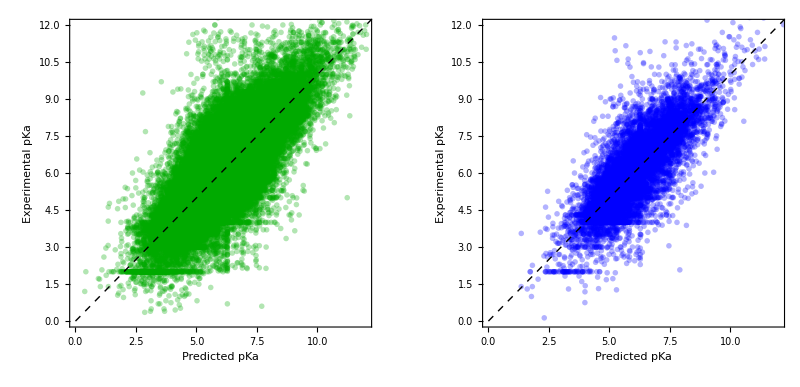

```mathematica
figure2
```

Figure 2: Correlation between the predicted and experimental pKa values for the PLAPT model, showcasing results for the training data (left) and test data (right). The dashed line indicates perfect prediction accuracy .

Based on Table 1, PLAPT exhibits very impressive generalization, essentially entirely eliminating overfitting, evidenced by the congruence of the Pearson correlation coefficients, approximately 0.8, across both training and test datasets. This level of performance consistency contrasts sharply with models such as OnionNet and , which demonstrate substantial overfitting (See Figure 3 and Figure 4). Our model’s stability is further supported by the minimal discrepancy between MSE and RMSE across the training and testing datasets (Table 1).

We attribute the robustness of PLAPT to its use of pretrained encoders—specifically ProtBERT and ChemBERTa—leveraged to abstract protein and molecule representations. These encoders were trained unsupervised on extensive datasets, meaning they contain transferable generalized understanding of the biochemical domain to PLAPT, mitigating the overfitting commonly encountered in models trained de novo on niche datasets.

In Figure 2, the data points’ proximity to the line of perfect prediction across both data sets further validates the model’s predictive reliability. The PLAPT model’s fidelity in its predictive performance, as demonstrated in these results, positions it as a substantial advancement in the field of computational affinity prediction.

Figure 3: A random forest (RF) based model’s correlation between experimentally measured dissociation rate constants (-log ) and the corresponding predicted values for: (A) training set, where N = 407, Rp = 0.968, and RMSE = 0.474; (B) validation set, where N = 102, Rp = 0.706, and RMSE = 0.986; (Huisi et al.)

Figure 4: OnionNet-2 predicted pKa with respect to experimentally determined pKa on (a) training set (b). (Zechen et al.)

As seen in Figure 3 and Figure 4, the Random Forest model and OnionNet-2 exhibit strong performance discrepancies between training and validation datasets, indicative of overfitting. Our PLAPT model, through the use of pre-trained encoders, achieves almost identically distributed predictions, indicating a high degree of generalization and no overfitting.

## Real World Example

Test out PLAPT on a novel protein-ligand pair.

```mathematica
testProtein=Entity["Protein","DEFB4"]
```

defensin, beta 4 precursor

Visualization

```mathematica
ProteinData[testProtein,"MoleculePlot"]
```

-Graphics3D-

```mathematica
testProteinSequence=testProtein["Sequence"]
```

MRVLYLLFSFLFIFLMPLPGVFGGIGDPVTCLKSGAICHPVFCPRRYKQIGTCGLPGTKCCKKP

A test molecule

```mathematica
testMolecule=Entity["Chemical","StearicAcid"];
```

```mathematica
MoleculePlot3D[testMolecule]
```

-Graphics3D-

```mathematica
testMoleculeSmiles=testMolecule["SMILES"]
```

CCCCCCCCCCCCCCCCCC(=O)O

Predict the binding affinity

```mathematica
affinity=PredictAffinity[testMolecule,testProtein]
```

<|neg_log10_affinity_M→6.14325,affinity_uM→0.719029|>

## Conclusion and Future Work

We have successfully demonstrated that the incorporation of pre-trained encoders is a viable strategy for mitigating overfitting in the domain of protein-ligand binding affinity prediction. This novel approach leverages the extensive knowledge already captured by models such as ProtBERT and ChemBERTa, which are pre-trained on large, unlabelled biochemical datasets. By using these encoders, PLAPT gains the ability to generalize across diverse datasets, which is of paramount importance in computational drug discovery, where the ability to accurately predict across a wide range of potential compounds is critical.

While the performance of PLAPT is on-par with current state-of-the-art methods, it is the means by which this performance is achieved that sets our approach apart. The model’s incorporation of pre-existing, extensive biochemical knowledge from the underlying encoders reduces its susceptibility to overfitting—a significant advancement.

### Further Work

In pursuit of enhancing the accuracy of our model while preserving its generalization capabilities, we propose two main avenues for further research. First, the aggregation of a more extensive dataset would provide a broader chemical space for the model to learn from, potentially refining its predictive accuracy. Second, the integration of a self - attention mechanism within the primary predictor could allow for more nuanced interpretation of the interplay between protein and ligand features. 

The self - attention mechanism, particularly, could enable the model to dynamically weigh the importance of different parts of the input data, potentially leading to more precise affinity predictions . We hypothesize that this addition, in concert with the robust foundation provided by the pre - trained encoders, will sustain the model' s generalization strength .

## Acknowledgements

We would like to extend our heartfelt thanks to our mentor, Nicolo Monti, for his insightful guidance throughout the project. Additionally, our gratitude goes to the entire WELP staff and the WELP program for granting us the opportunity to undertake this project, which has been an enriching exploration in the field of machine learning.

## References

Chithrananda, S., Grand, G., & Ramsundar, B. (2020). ChemBERTa: Large-Scale Self-Supervised Pretraining for Molecular Property Prediction. Retrieved from https://arxiv.org/abs/2010.09885

database, Pdb.-C. (n.d.). Welcome to pdbbind-CN database. Retrieved December 16, 2023, from http://pdbbind.org.cn/index.php

Elnaggar, A., Heinzinger, M., Dallago, C., Rehawi, G., Wang, Y., Jones, L., Gibbs, T., Feher, T., Angerer, C., Steinegger, M., Bhowmik, D., & Rost, B. (2021). ProtTrans: Towards Cracking the Language of Life’s Code Through Self-Supervised Learning. bioRxiv. https://www.biorxiv.org/content/10.1101/2020.07.12.199554v3

Huisi L; Minyi S; Hai-Xia L; Renxiao Wang; (2022). Public Data Set of Protein–Ligand Dissociation Kinetic Constants for Quantitative Structure–Kinetics Relationship Studies. Retrieved from https://pubs.acs.org/doi/10.1021/acsomega.2c02156

Jglaser/binding_affinity · datasets at hugging face. (n.d.). jglaser/binding_affinity · Datasets at Hugging Face. Retrieved December 16, 2023, from https://huggingface.co/datasets/jglaser/binding_affinity/viewer/default/train

Jin Z;Wu T;Chen T;Pan D;Wang X;Xie J;Quan L;Lyu Q; (n.d.). CAPLA: Improved prediction of protein-ligand binding affinity by a deep learning approach based on a cross-attention mechanism. Bioinformatics (Oxford, England). U.S. National Library of Medicine. Retrieved December 16, 2023, from https://pubmed.ncbi.nlm.nih.gov/36688724/

Liangzhen Zheng, Jingrong Fan, and Yuguang Mu. OnionNet: A multiple-layer intermolecular-contact ... - ACS publications. Retrieved December 17, 2023, from https://pubs.acs.org/doi/10.1021/acsomega.9b01997

Wang H;Liu H;Ning S;Zeng C;Zhao Y; (n.d.). DLSSAffinity: Protein-ligand binding affinity prediction via a deep learning model. Physical chemistry chemical physics : PCCP. U.S. National Library of Medicine. Retrieved December 16, 2023, from https://pubmed.ncbi.nlm.nih.gov/35416807/

Zhenglz. (n.d.). Zhenglz/onionnet: A multiple-layer inter-molecular contact features based deep neural network for protein-ligand binding affinity prediction. GitHub. Retrieved December 16, 2023, from https://github.com/zhenglz/onionnet/

## Appendix

All our code can be found on our Github repository: https://github.com/trrt-good/WELP-PLAPT

All our data and models can be found on our Google Drive: https://drive.google.com/drive/folders/1e-ujgHx5bW0JKxSZY5u34As77o4-IIFs?usp=sharing